## As always some code

```mathematica
SolutionMatrix[g_]:=Block[{mat,size, ordered},
size=VertexCount[g];
ordered=Range[VertexCount[g]];
mat=Table[
Table[
If[row==col,2,
If[EdgeQ[g,row<->col],1,0]
]
,
{col,ordered}
]
,
{row,ordered}
];
mat
]
```

```mathematica
DrawSolutionMatrix[g_]:=Block[{mat=SolutionMatrix[g],  labels, size,  start,newBucket},
size=VertexCount[g];
labels=Table[{k,Block[{res=Style[k,Bold]},
res]},{k,size}];
start=1;
Column[
{
(*Graph[g,ImageSize->500,VertexStyle->colors]
,*)
MatrixPlot[Take [ mat,5],Mesh->All, ImageSize->500,FrameTicks->{labels,labels,labels,labels}]
}
]
]
```

```mathematica
DrawSolutionMatrix[g_,merges_]:=Block[{mat=SolutionMatrix[g],  labels, size,  start,newBucket},
size=VertexCount[g];
labels=Table[{k,Block[{res=Style[k,Bold]},
res]},{k,size}];
start=1;
Table[
Table[
mat[[v,m[[1]]]]=Max[mat[[v,m[[1]]]],mat[[v,m[[2]]]]];
mat[[m[[1]],v]]=mat[[v,m[[1]]]];
mat[[m[[2]],v]]=mat[[m[[1]],v]];
mat[[v,m[[2]]]]=mat[[m[[2]],v]];
,{v,size}
]
,{m,merges}
];
Column[
{
(*Graph[g,ImageSize->500,VertexStyle->colors]
,*)
MatrixPlot[mat,Mesh->All, ImageSize->500,FrameTicks->{labels,labels,labels,labels}]
}
]
]
```

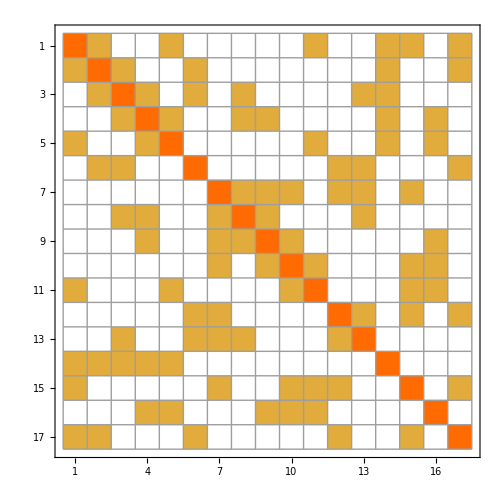

```mathematica
DrawSolutionMatrix[plantri8,{}]
```

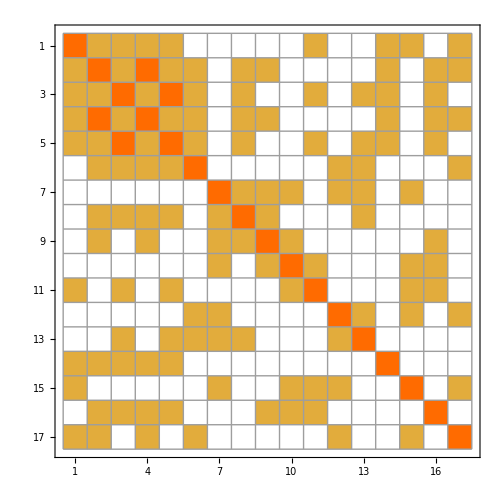

```mathematica
DrawSolutionMatrix[plantri8,{{2,4},{3,5}}]
```

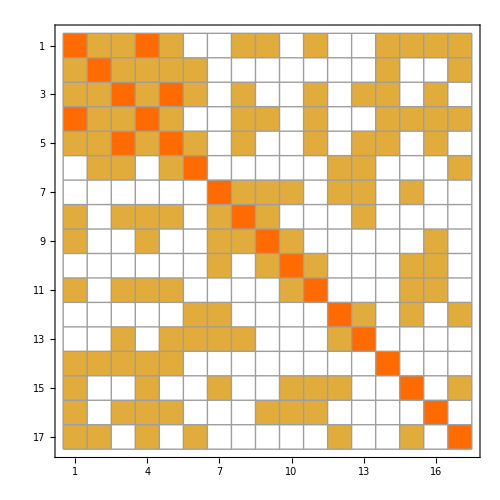

```mathematica
DrawSolutionMatrix[plantri8,{{1,4},{3,5}}]
```

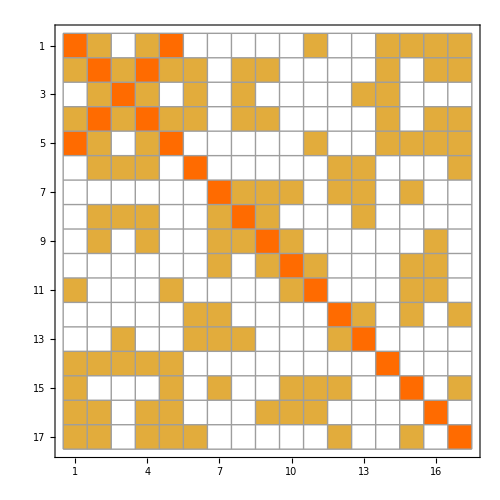

```mathematica
DrawSolutionMatrix[plantri8,{{1,5},{2,4}}]
```

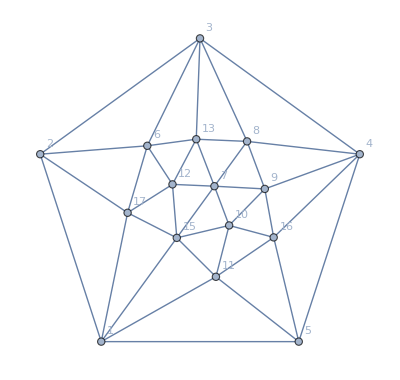

```mathematica
Graph[VertexDelete[plantri8,14],VertexLabels->"Name"]
```